To ASEN 5007 students: upon downloading this Notebook, check it out by following this procedure.
1.  Compile the initialization cells (1 through 6).  For Mathematica versions <6, use
          Kernel -> Evaluation -> Evaluate Initialization. 
      For  Mathematica versions 6 or higher, use
          Kernel-> Evaluate Initialization Cells
     (To get rid of annoying warning messages, you should initialize twice. )
     Verify that the output  of the initialized cells,  which is  generated by the test statements in blue,
      looks OK, i.e. agrees with Chapter 21 Figures.
2.  Pick Cell 7 by clicking mouse on interior of cell.  Execute by pressing <Shift-Enter> on a
     Windows PC or newer Macs, <Enter> on older Macs.  Check that answers agree with Chapter21.
3.  Do HW Exercise 10.3 (transmission tower) by writing scripts in Cell 8 using  Cell 7 as "template"
     Recommended settings for plot arguments such as view and box are given in that cell
     The weight of the truss can be obtained by running Cell 10, and compared with value in Notes.

Cell 1: Module to assemble master stiffness matrix of a plane truss.
The element stiffness module that supports the assembler  is described in Chapter 20.

```mathematica
SpaceTrussMasterStiffness[nodxyz_,elenod_,
   elemat_,elefab_,prcopt_]:=Module[
  {numele=Length[elenod],numnod=Length[nodxyz],neldof,
  e,eftab,ni,nj,i,j,ii,jj,ncoor,Em,A,options,Ke,K},
  K=Table[0,{3*numnod},{3*numnod}];
  For [e=1, e<=numele, e++, {ni,nj}=elenod[[e]]; 
      eftab={3*ni-2,3*ni-1,3*ni,3*nj-2,3*nj-1,3*nj}; 
      ncoor={nodxyz[[ni]],nodxyz[[nj]]};         
      Em=elemat[[e]]; A=elefab[[e]]; options=prcopt;  
      Ke=SpaceBar2Stiffness[ncoor,Em,A,options];
      neldof=Length[Ke];
      For [i=1, i<=neldof, i++, ii=eftab[[i]];
          For [j=i, j<=neldof, j++, jj=eftab[[j]];
              K[[jj,ii]]=K[[ii,jj]]+=Ke[[i,j]] ];
          ];
      ]; Return[K];
  ];
SpaceBar2Stiffness[ncoor_,Em_,A_,options_]:=Module[
  {x1,x2,y1,y2,z1,z2,x21,y21,z21,EA,numer,L,LL,LLL,Ke}, 
  {{x1,y1,z1},{x2,y2,z2}}=ncoor; {x21,y21,z21}={x2-x1,y2-y1,z2-z1};
  EA=Em*A; {numer}=options;  LL=x21^2+y21^2+z21^2; L=Sqrt[LL];
  If [numer,{x21,y21,z21,EA,LL,L}=N[{x21,y21,z21,EA,LL,L}]];
  If [!numer, L=PowerExpand[L]]; LLL=Simplify[LL*L];
  Ke=(Em*A/LLL)*
     {{ x21*x21, x21*y21, x21*z21,-x21*x21,-x21*y21,-x21*z21},
      { y21*x21, y21*y21, y21*z21,-y21*x21,-y21*y21,-y21*z21},
      { z21*x21, z21*y21, z21*z21,-z21*x21,-z21*y21,-z21*z21},
      {-x21*x21,-x21*y21,-x21*z21, x21*x21, x21*y21, x21*z21},
      {-y21*x21,-y21*y21,-y21*z21, y21*x21, y21*y21, y21*z21},
      {-z21*x21,-z21*y21,-z21*z21, z21*x21, z21*y21, z21*z21}};
  Return[Ke]];
  
ClearAll[nodxyz,elemat,elefab,eleopt];
nodxyz={{0,0,0},{10,0,0},{10,10,0}};
elenod= {{1,2},{2,3},{1,3}};
elemat= Table[100,{3}]; elefab= {1,1/2,2*Sqrt[2]}; prcopt= {False};
K=SpaceTrussMasterStiffness[nodxyz,elenod,elemat,elefab,prcopt];
Print["Master Stiffness of Example Truss in 3D:\n",K//MatrixForm];
Print["eigs of K (should show 6 zeros): ",Chop[Eigenvalues[N[K]]]];
```

Master Stiffness of Example Truss in 3D:
(20 | 10 | 0 | -10 | 0 | 0 | -10 | -10 | 0
10 | 10 | 0 | 0 | 0 | 0 | -10 | -10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-10 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | -5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-10 | -10 | 0 | 0 | 0 | 0 | 10 | 10 | 0
-10 | -10 | 0 | 0 | -5 | 0 | 10 | 15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

eigs of K (should show 6 zeros): {45.3577,16.7403,7.902,0,0,0,0,0,0}

Cell 2:  Modules to apply homogeneous, single-freedom displacement BCs on master stiffness and forces.
Prescribed nonzero displacements are allowed. These modules also work, without any change, for more general FEM models.

```mathematica
AppliedForceVector[nodtag_,nodval_]:= Module[{i,ftag,fval,
 numdof,f}, {ftag,fval}={Flatten[nodtag],Flatten[nodval]};
 numdof=Length[ftag]; f=Table[0,{numdof}]; 
 For [i=1,i<=numdof,i++, If [ftag[[i]]==0, f[[i]]=fval[[i]]]];
 Return[f]]; 

ModifiedMasterStiffness[nodtag_,K_] := Module[
 {i,j,k,n=Length[K],pdof,np,Kmod=K},
  pdof=PrescDispDOFTags[nodtag]; np=Length[pdof]; 
  For [k=1,k<=np,k++, i=pdof[[k]]; 
      For [j=1,j<=n,j++, Kmod[[i,j]]=Kmod[[j,i]]=0];
      Kmod[[i,i]]=1]; 
  Return[Kmod]];  
  
ModifiedNodeForces[nodtag_,nodval_,K_,f_]:= Module[
 {i,j,k,n=Length[K],pdof,pval,np,d,c,fmod=f},
  pdof=PrescDispDOFTags[nodtag]; np=Length[pdof]; 
  pval=PrescDispDOFValues[nodtag,nodval]; c=Table[1,{n}]; 
  For [k=1,k<=np,k++, i=pdof[[k]]; c[[i]]=0];
  For [k=1,k<=np,k++, i=pdof[[k]]; d=pval[[k]]; 
      fmod[[i]]=d; If [d==0, Continue[]];
      For [j=1,j<=n,j++, fmod[[j]]-=K[[i,j]]*c[[j]]*d]; 
      ];  ClearAll[c]; 
  Return[fmod]];
  
PrescDispDOFTags[nodtag_]:= Module[
  {j,n,numnod=Length[nodtag],pdof={},k=0,m},
  For [n=1,n<=numnod,n++, m=Length[nodtag[[n]]];
      For [j=1,j<=m,j++, If [nodtag[[n,j]]>0, 
                AppendTo[pdof,k+j]]]; k+=m;
      ]; Return[pdof]]; 
     
PrescDispDOFValues[nodtag_,nodval_]:= Module[
 {j,n,numnod=Length[nodtag],pval={},k=0,m},
  For [n=1,n<=numnod,n++, m=Length[nodtag[[n]]];
      For [j=1,j<=m,j++, If [nodtag[[n,j]]>0, 
                AppendTo[pval,nodval[[n,j]]]]]; k+=m;
      ]; Return[pval]];
     
nodtag={{1,1,1},{0,0,1}}; nodval={{-1,2,0},{0,3,0},{2,1,0}};
K={{K11,K12,K13,K14,K15,K16},{K12,K22,K23,K24,K25,K26}, 
   {K13,K23,K33,K34,K35,K36},{K14,K24,K34,K44,K45,K46},
   {K15,K25,K35,K45,K55,K56},{K16,K26,K36,K46,K56,K66}};
Print["K before BC:",K//MatrixForm];
f=AppliedForceVector[nodtag,nodval];
Print["f before BC:",f];    
Kmod=ModifiedMasterStiffness[nodtag,K];
Print["K modified for BC:",Kmod//MatrixForm];
fmod=ModifiedNodeForces[nodtag,nodval,K,f];
Print["f modified for BC:",fmod];
```

K before BC:(K11 | K12 | K13 | K14 | K15 | K16
K12 | K22 | K23 | K24 | K25 | K26
K13 | K23 | K33 | K34 | K35 | K36
K14 | K24 | K34 | K44 | K45 | K46
K15 | K25 | K35 | K45 | K55 | K56
K16 | K26 | K36 | K46 | K56 | K66)

f before BC:{0,0,0,0,3,0}

K modified for BC:(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | K44 | K45 | 0
0 | 0 | 0 | K45 | K55 | 0
0 | 0 | 0 | 0 | 0 | 1)

f modified for BC:{-1,2,0,K14-2 K24,3+K15-2 K25,0}

Cell 3:  Modules to get internal forces and stresses in plane truss members

```mathematica
SpaceTrussIntForces[nodxyz_,elenod_,elemat_,elefab_,
  noddis_,prcopt_]:= Module[{  numnod=Length[nodxyz],
  numele=Length[elenod],e,ni,nj,ncoor,Em,A,options,ue,p},
  p=Table[0,{numele}]; 
  For [e=1, e<=numele, e++, {ni,nj}=elenod[[e]]; 
      ncoor={nodxyz[[ni]],nodxyz[[nj]]}; 
      ue=Flatten[{ noddis[[ni]],noddis[[nj]] }];          
      Em=elemat[[e]]; A=elefab[[e]]; options=prcopt; 
      p[[e]]=SpaceBar2IntForce[ncoor,Em,A,ue,options]
      ]; 
  Return[p]];

SpaceBar2IntForce[ncoor_,Em_,A_,ue_,options_]:= Module[ 
 {x1,x2,y1,y2,z1,z2,x21,y21,z21,EA,numer,LL,pe}, 
 {{x1,y1,z1},{x2,y2,z2}}=ncoor; {x21,y21,z21}={x2-x1,y2-y1,z2-z1};
  EA=Em*A; {numer}=options;  LL=x21^2+y21^2+z21^2;
  If [numer,{x21,y21,z21,EA,LL}=N[{x21,y21,z21,EA,LL}]];
  pe=(EA/LL)*(x21*(ue[[4]]-ue[[1]])+y21*(ue[[5]]-ue[[2]])+
             +z21*(ue[[6]]-ue[[3]]));
  Return[pe]]; 
  
SpaceTrussStresses[elefab_,elefor_,prcopt_]:= Module[
 {numele=Length[elefab],e,elesig}, elesig=Table[0,{numele}]; 
  For [e=1, e<=numele, e++, elesig[[e]]=elefor[[e]]/elefab[[e]] ];
  Return[elesig]]; 

ClearAll[nodxyz,elenod,elemat,elefab,noddis];
nodxyz={{0,0,0},{10,0,0},{10,10,0}}; elenod={{1,2},{2,3},{1,3}};
elemat= Table[100,{3}]; elefab= {1,1/2,2*Sqrt[2]};
noddis={{0,0,0}, {0,0,0}, {4/10,-2/10,0}}; prcopt={False};
elefor=SpaceTrussIntForces[nodxyz,elenod,elemat,elefab,noddis,prcopt];
Print["Int Forces of Example Truss in 3D:",elefor];
Print["Stresses:",SpaceTrussStresses[elefab,elefor,prcopt]];
```

Int Forces of Example Truss in 3D:{0,-1,2 √2}

Stresses:{0,-2,1}

Cell 4.  Print utilities supporting print output and some array-partition transformations

```mathematica
PrintSpaceTrussNodeCoordinates[nodxyz_,title_,digits_]:= Module[
  {numnod=Length[nodxyz],n,x,y,z,d=6,f=6,tab}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++,{x,y,z}=nodxyz[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[x,{d,f}],PaddedForm[y,{d,f}],
                 PaddedForm[z,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},   
      TableDirections->{Column,Row},TableSpacing->{0,2},
      TableHeadings ->{None,{"node", "x-coor", "y-coor", "z-coor"}}]];
   ];
   
PrintSpaceTrussElementData[elenod_,elemat_,elefab_,title_,digits_]:= Module[
  {e,numele=Length[elenod],Em,A,d=6,f=3,tab}, 
  tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, Em=elemat[[e]]; A=elefab[[e]];
        tab[[e]]={ToString[e],ToString[elenod[[e]]],
             PaddedForm[Em,{d,f}],PaddedForm[A,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,2},
         TableHeadings ->{None,{"elem", "nodes", "modulus", "area"}}]];
   ];
   
PrintSpaceTrussFreedomActivity[nodtag_,nodval_,title_,digits_]:= Module[
  {numnod=Length[nodtag],n,tag,val,tab}, 
   tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, t=nodtag[[n]]; v=nodval[[n]];
        tab[[n]]={ToString[n],
          PaddedForm[t[[1]]],PaddedForm[t[[2]]],PaddedForm[t[[3]]],
          PaddedForm[v[[1]]],PaddedForm[v[[2]]],PaddedForm[v[[3]]] }];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-tag", "y-tag", "z-tag",
                          "x-value", "y-value", "z-value"}} ]];
   ];

PrintSpaceTrussNodeDisplacements[noddis_,title_,digits_]:= Module[
  {numnod=Length[noddis],n,ux,uy,uz,tab,d=6,f=6}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, {ux,uy,uz}=noddis[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[ux,{d,f}],
                 PaddedForm[uy,{d,f}],PaddedForm[uz,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-displ", "y-displ", "z-displ"}}]];
   ];
PrintSpaceTrussNodeForces[nodfor_,title_,digits_]:= Module[
  {numnod=Length[nodfor],n,fx,fy,fz,tab,d=4,f=4}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, {fx,fy,fz}=nodfor[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[fx,{d,f}],
                 PaddedForm[fy,{d,f}],PaddedForm[fz,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-force", "y-force", "z-force"}}]];
   ];
   
PrintSpaceTrussElemForcesAndStresses[elefor_,elesig_,title_,digits_]:= 
  Module[{numele=Length[elefor],e,p,s,d=4,f=4,tab}, 
   tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, p=elefor[[e]]; s=elesig[[e]];
       tab[[e]]={ToString[e],PaddedForm[p,{d,f}],PaddedForm[s,{d,f}]} ]; 
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1}, 
         TableHeadings ->{None,{"elem", "axial force", "axial stress"}}]];
   ]; 
 
FlatNodePartVector[nv_]:=Flatten[nv];
           
NodePartFlatVector[nfc_,v_]:= Module [
  {i,k,m,n,nv={},numnod},
  If [Length[nfc]==0, nv=Partition[v,nfc]];
  If [Length[nfc]>0,  numnod=Length[nfc]; m=0;
      nv=Table[0,{numnod}];   
      For [n=1,n<=numnod,n++, k=nfc[[n]]; 
          nv[[n]]=Table[v[[m+i]],{i,1,k}]; 
          m+=k]];
  Return[nv]];

nodxyz={{0,0,0},{10,0,0},{10,10,0}};
PrintSpaceTrussNodeCoordinates[nodxyz,"Test node coord print",{6,4}];
elenod={{1,2},{2,3},{1,3}}; elemat={100,100,100}; elefab=N[{1,1/2,2*Sqrt[2]}];
PrintSpaceTrussElementData[elenod,elemat,elefab,"Test elem data print",{7,3}];
nodtag={{1,1,1},{0,1,1},{0,0,1}}; nodval={{0,0,0},{0,0,0},{2,1,0}};
PrintSpaceTrussFreedomActivity[nodtag,nodval,"Test DOF activity print",{}];
noddis={{0,0,0},{0,0,0},{0.4,-0.2,0}}; 
PrintSpaceTrussNodeDisplacements[noddis,"Test node disp print",{}];
nodfor={{0,0,0},{0,0,0},{2,1,0}}; 
PrintSpaceTrussNodeForces[nodfor,"Test node force print",{8,4}];
elefor={3,4,5}; elesig={3,2,2.5};
PrintSpaceTrussElemForcesAndStresses[elefor,elesig,"Test elem force & stress print",{}];
u={1,2,3,4,5,6}; noddis=NodePartFlatVector[2,u];
Print["u=",u,",  noddis=",noddis//MatrixForm];
```

Test node coord print

node | x-coor | y-coor | z-coor
1 |       0 |       0 |       0
2 |      10 |       0 |       0
3 |      10 |      10 |       0

Test elem data print

elem | nodes | modulus | area
1 | {1, 2} |      100 |     1.000
2 | {2, 3} |      100 |     0.500
3 | {1, 3} |      100 |     2.828

Test DOF activity print

node | x-tag | y-tag | z-tag | x-value | y-value | z-value
1 |  1 |  1 |  1 |  0 |  0 |  0
2 |  0 |  1 |  1 |  0 |  0 |  0
3 |  0 |  0 |  1 |  2 |  1 |  0

Test node disp print

node | x-displ | y-displ | z-displ
1 |       0 |       0 |       0
2 |       0 |       0 |       0
3 |  0.400000 | -0.200000 |       0

Test node force print

node | x-force | y-force | z-force
1 |         0 |         0 |         0
2 |         0 |         0 |         0
3 |         2 |         1 |         0

Test elem force & stress print

elem | axial force | axial stress
1 |     3 |     3
2 |     4 |     2
3 |     5 |  2.5000

u={1,2,3,4,5,6},  noddis=(1 | 2
3 | 4
5 | 6)

Cell 5A.  Plot of elements and nodes of space truss model.  Cell also contains utility 
WorldScreenMatrix that supports postprocessing plots in Cells 5B and 5C

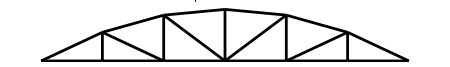

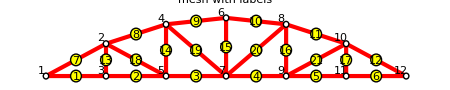

```mathematica
WorldToScreenMatrix[view_]:=Module[{VW={{0,1,0},{0,0,1}},
  Vx,Vy,Vz,Wx,Wy,Wz,xden,yden,Q}, 
  If [Length[view]==2, VW=view];
  If [Length[view]==3, VW[[2]]=view];
  {{Vx,Vy,Vz},{Wx,Wy,Wz}}=VW;
  xden=Sqrt[Wz^2*(Vx^2+Vy^2)-2*Wx*Wz*Vx*Vz-
  2*Wy*Vy*(Wx*Vx+Wz*Vz)+Wy^2*(Vx^2+Vz^2)+Wx^2*(Vy^2+Vz^2)];
  yden=Sqrt[(Wx^2+Wy^2+Wz^2)*(Wz^2*(Vx^2+Vy^2)-2*Wx*Wz*Vx*Vz-
  2*Wy*Vy*(Wx*Vx+Wz*Vz)+Wy^2*(Vx^2+Vz^2)+Wx^2*(Vy^2+Vz^2))];
  Q={{Wz*Vy-Wy*Vz,-Wz*Vx+Wx*Vz,Wy*Vx-Wx*Vy}/xden, 
     {Wy^2*Vx-Wx*Wy*Vy+Wz*(Wz*Vx-Wx*Vz),-Wx*Wy*Vx+Wx^2*Vy+ 
      Wz*(Wz*Vy-Wy*Vz),-Wz*(Wx*Vx+Wy*Vy)+(Wx^2+Wy^2)*Vz}/yden};
  Return[Q]];

PlotSpaceTrussElements[nodxyz_,elenod_,title_,
 {view_,aspect_,imgsiz_,labels_}]:= 
  Module[{numnod=Length[nodxyz],numele=Length[elenod],e,n,
  ni,nj,Q,x,y,xmin,xmax,ymin,ymax,dx,dy,xyc,ar,dfun,pbars={}},
  x=y=Table[0,{numnod}]; Q=WorldToScreenMatrix[view];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
  {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}];
  {dx,dy}={xmax-xmin,ymax-ymin};
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
       xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};      
       AppendTo[pbars,Graphics[Line[xyc]]]
      ];
 arat=AspectRatio->Automatic; If [aspect>0, arat=AspectRatio->aspect];
 If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
 dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
 Show[Graphics[AbsoluteThickness[2]],
      Graphics[RGBColor[0,0,0]],
      pbars, arat, PlotLabel->title,
      ImageSize->imgsiz,DisplayFunction->dfun ];
 ClearAll[pbars];
 ];

PlotSpaceTrussElementsAndNodes[nodxyz_,elenod_,title_,
   {view_,aspect_,imgsiz_,labels_}]:= Module[{numnod=Length[nodxyz],
  numele=Length[elenod],k=Length[labels],e,n,ni,nj,Q,x,y,xyc,
  xy0,xyn,xmin,xmax,ymin,ymax,elabels,nlabels,fntinfo,
  labnod,frn,fex,fey,labele,fre,fntnam,fntsiz,fntwgt,fntslt,
  black,red,green,blue,yellow,fill,grey,nofill,arat,
  style,dx,dy,dmin,rn,re,ex,ey,elab,nlab,dfun,pbars={},
  pecirc={},pelab={},pedisk={},pncirc={},pndisk={},pnlab={} },
  x=y=Table[0,{numnod}]; Q=WorldToScreenMatrix[view];
  {labnod,frn,fex,fey,labele,fre,fntnam,fntsiz,fntwgt,fntslt}=
    {True,0.03,-1.5,0.8,True,0.03,"Times",12,"Plain","Plain"};  
  If [k>=1, nlabels=labels[[1]] ]; 
  If [k>=2, elabels=labels[[2]] ];
  If [k>=3, fntinfo=labels[[3]] ];
  If [Length[nlabels]>=1, labnod=nlabels[[1]] ];
  If [Length[nlabels]>=2, frn=   nlabels[[2]] ];
  If [Length[nlabels]>=3, fex=   nlabels[[3]] ];
  If [Length[nlabels]>=4, fey=   nlabels[[4]] ];
  If [Length[elabels]>=1, labele=elabels[[1]] ];
  If [Length[elabels]>=2, fre=   elabels[[2]] ];
  If [Length[fntinfo]>=1, fntnam=fntinfo[[1]] ];
  If [Length[fntinfo]>=2, fntsiz=fntinfo[[2]] ];
  If [Length[fntinfo]>=3, fntwgt=fntinfo[[3]] ];
  If [Length[fntinfo]>=4, fntslt=fntinfo[[4]] ];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
  {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}];
  {dx,dy}={xmax-xmin,ymax-ymin}; dmin=Min[dx,dy];
  rn=frn*dmin; re=fre*dmin;
  style=TextStyle->{FontFamily->fntnam,FontSize-> fntsiz,
                    FontWeight->fntwgt,FontSlant->fntslt};
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
      xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};
      xy0=(xyc[[1]]+xyc[[2]])/2;
      AppendTo[pbars,Graphics[Line[xyc]]];
      If [labele, elab=ToString[e];
          AppendTo[pedisk, Graphics[Disk[xy0,re]]]; 
          AppendTo[pecirc, Graphics[Circle[xy0,re]]];
          AppendTo[pelab,  Graphics[Text[elab,xy0-{0,0.2*re},style]]]
         ];
      ];
  style=TextStyle->{FontFamily->fntnam,FontSize-> fntsiz,
                    FontWeight->"Bold",FontSlant->"Plain"};
  For [n=1,n<=numnod,n++,  xyn={x[[n]],y[[n]]}; 
      AppendTo[pndisk,  Graphics[Disk[xyn,rn]]];
      AppendTo[pncirc,  Graphics[Circle[xyn,rn]]];
      If [labnod, nlab=ToString[n]; xy0=xyn+{fex,fey}*rn; 
          AppendTo[pnlab, Graphics[Text[nlab,xy0,style]]]];
     ]; 
  {black,red,green,blue,yellow}={RGBColor[0,0,0],RGBColor[1,0,0],
     RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,1,0]};
  {nofill,grey,fill}={GrayLevel[0],GrayLevel[.8],GrayLevel[1]};
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
  Show[Graphics[nofill],Graphics[AbsoluteThickness[3]],
       Graphics[red],pbars, Graphics[AbsoluteThickness[1]],
       Graphics[fill],pndisk, Graphics[nofill],pncirc, 
       Graphics[yellow], pedisk, Graphics[nofill], 
       Graphics[black], pecirc, pelab, pnlab,
       arat, PlotLabel->title,ImageSize->imgsiz,
       DisplayFunction->dfun ];
   ClearAll[pbars,pndisk,pncirc,pedisk,pecirc,pelab];
 ];
 
nodxyz={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
       {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
nodxyz=N[nodxyz];
elenod={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
        {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
        {2,3},{4,5},{6,7},{8,9},{10,11},
        {2,5},{4,7},{7,8},{9,10}};
view={{0,1,0},{0,0,1}}; imgsiz=450;
PlotSpaceTrussElements[nodxyz,elenod,"plain mesh",{view,0,imgsiz,{}}];
labels={{True,0.05,-1.8,1.8},{True,0.10},{"Times",12,"Plain","Italic"}};
PlotSpaceTrussElementsAndNodes[nodxyz,elenod,"mesh with labels",
       {view,-1,imgsiz,labels}];
```

Cell 5B.  PlotSpaceTrussDeformedShape does exactly what it says.  Note: argument amplif can be
a scalar amplification, or a list of amplifications.  If the latter, a sequence of colors is used.

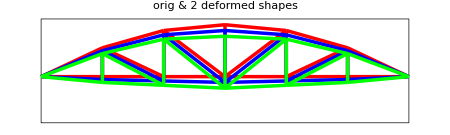

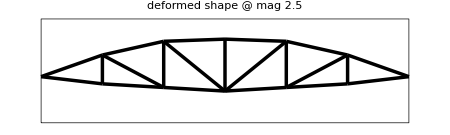

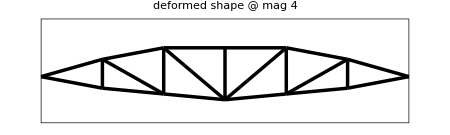

```mathematica
PlotSpaceTrussDeformedShape[nodxyz_,elenod_,noddis_,
    amplif_,box_,title_,{view_,aspect_,imgsiz_,colors_}]:= 
  Module[{numnod=Length[nodxyz],numele=Length[elenod],a={},c={},e,k,m,n,
  ni,nj,nf,Q,xbox,ybox,x,y,x0,y0,xmin,xmax,ymin,ymax,dx,dy,xyc,arat,dfun,
  black,red,green,blue,yellow,white,fill,grey,nofill,f,pbars={},p={}},
  Q=WorldToScreenMatrix[view]; x=y=Table[0,{numnod}]; nf=Length[box]; 
  If [nf>0, xbox=ybox=Table[0,{nf}]; 
      For [n=1,n<=nf,n++, {xbox[[n]],ybox[[n]]}=Q.box[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[xbox],Max[xbox],Min[ybox],Max[ybox]}] ];      
  If [nf==0,
      For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}] ];
  {dx,dy}={xmax-xmin,ymax-ymin};
  {black,red,green,blue,yellow,white}={RGBColor[0,0,0],RGBColor[1,0,0],
     RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,1,0],RGBColor[1,1,1]};
  {nofill,grey,fill}={GrayLevel[0],GrayLevel[.8],GrayLevel[1]};
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  AppendTo[p,Graphics[AbsoluteThickness[.5]]]; AppendTo[p,Graphics[nofill]];
  enclosingbox={{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}};
  AppendTo[p,Graphics[Line[enclosingbox]]]; 
  AppendTo[p,Graphics[AbsoluteThickness[2.5]]];
  If [Length[amplif]==0,a={amplif},a=amplif];
  If [Length[colors]==0,c={colors},c=colors]; k=Length[c];
  AppendTo[p,Graphics[black]];
  For [m=1,m<=Length[a],m++, f=a[[m]]; color=c[[Min[m,k]]];
       If [color=="black",  AppendTo[p,Graphics[black]]];
       If [color=="red",    AppendTo[p,Graphics[red]]];
       If [color=="blue",   AppendTo[p,Graphics[blue]]];
       If [color=="green",  AppendTo[p,Graphics[green]]];
       If [color=="yellow", AppendTo[p,Graphics[yellow]]];
       If [color=="white",  AppendTo[p,Graphics[white]]];
       For [n=1,n<=numnod,n++, 
           {x[[n]],y[[n]]}=Q.(nodxyz[[n]]+f*noddis[[n]])];
       For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
            xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};      
       AppendTo[p,Graphics[Line[xyc] ]]];
      ];
 dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
 Show[p, arat, PlotLabel->title, ImageSize->imgsiz,
      DisplayFunction->dfun ]; 
 ClearAll[x,y,xbox,ybox,p]; 
 ];
 

nodxyz={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
       {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
noddis={{0,0,0},{0,-10,0},{0,-10,0},{0,-15,0},{0,-15,0},{0,-20,0},
       {0,-20,0},{0,-15,0},{0,-15,0},{0,-10,0},{0,-10,0},{0,0,0}}/20;
nodxyz=N[nodxyz]; imgsiz=450;
elenod={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
        {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
        {2,3},{4,5},{6,7},{8,9},{10,11},
        {2,5},{4,7},{7,8},{9,10}};
view={{0,1,0},{0,0,1}}; box={{0,-8,0},{60,-8,0},{60,10,0},{0,10,0}};
PlotSpaceTrussDeformedShape[nodxyz,elenod,noddis,{0,1,2},
   box,"orig & 2 deformed shapes",{view,-1,imgsiz,{"red","blue","green"}}]; 
PlotSpaceTrussDeformedShape[nodxyz,elenod,noddis,2.5,box,
   "deformed shape @ mag 2.5",{view,-1,imgsiz,"black"}]; 
PlotSpaceTrussDeformedShape[nodxyz,elenod,noddis,4.0,box,
  "deformed shape @ mag 4",{view,-1,imgsiz,"black"}];
```

Cell 5C.  PlotSpaceTrussStresses level displays stress level and sign using color: red for tension,
blue for compression, white for zero stress.  A black backgroundset by GrayLevel[0.1] is used.

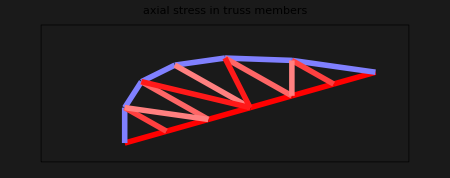

```mathematica
PlotSpaceTrussStresses[nodxyz_,elenod_,elesig_,sigfac_,box_,
      title_,{view_,aspect_,imgsiz_,labels_}]:=Module[
 {numele=Length[elenod],numnod=Length[nodxyz],
  e,n,ni,nj,nc,nf,xyc,x,y,xbox,ybox,xmin,xmax,ymin,ymax,dx,dy,
  smin,smax,fmax,sval,c1,c2,c3,arat,dfun,pbox={},pbars={}},
  x=y=Table[0,{numnod}]; Q=WorldToScreenMatrix[view]; nf=Length[box];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
  If [nf>0, xbox=ybox=Table[0,{nf}]; 
      For [n=1,n<=nf,n++, {xbox[[n]],ybox[[n]]}=Q.box[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[xbox],Max[xbox],Min[ybox],Max[ybox]}] ];      
  If [nf==0,
      {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}] ];
  {dx,dy}={xmax-xmin,ymax-ymin};
  AppendTo[pbox,Graphics[AbsoluteThickness[.5]]]; 
  AppendTo[pbox,Graphics[GrayLevel[0]]];
  enclosingbox={{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}};
  AppendTo[pbox,Graphics[Line[enclosingbox]]];
  AppendTo[pbox,Graphics[AbsoluteThickness[4]]]; 
  smin=Min[elesig]; smax=Max[elesig]; fmax=Max[Abs[smax],Abs[smin]];
  For [e=1,e<=numele,e++, 
     sval=N[elesig[[e]]*sigfac]; {c1,c2,c3}=LineColor[sval,fmax]; 
     {ni,nj}=elenod[[e]]; xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};    
     AppendTo[pbars,Graphics[RGBColor[c1,c2,c3]]];
     AppendTo[pbars,Graphics[Line[xyc]]]
     ];
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  dfun=If [$VersionNumber>=6.0, Print, $DisplayFunction];
  Show[pbox,Graphics[RGBColor[0,0,0]],pbars, 
       Background->GrayLevel[0.1],arat,PlotLabel->title,
       ImageSize->imgsiz,DisplayFunction->dfun ];
  ClearAll[pbars,x,y];
  ];

LineColor[f_,fmax_]:= Module[{r,RGBmax={1,0,0},  
   RGBmin={0,0,1}, RGBzero={1,1,1}, RGBout={0,0,0}},
   If [f==0 || fmax==0,   
       Return[RGBzero]];  (* White if f=0 *)
   If [f>fmax || f<-fmax, 
       Return[RGBout ]];  (* Black if outside range *)
   If [f>0, r= N[f/fmax]; 
       Return[r*RGBmax+(1-r)*RGBzero]]; (* positive *)
   If [f<0, r=-N[f/fmax]; 
       Return[r*RGBmin+(1-r)*RGBzero]]; (* negative *)
];

nodxyz={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
       {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
elenod= {{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
         {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
         {2,3},{4,5},{6,7},{8,9},{10,11},
         {2,5},{4,7},{7,8},{9,10}};
elesig={20,20,20,20,20,20,-10,-10,-10,-10,-10,-10,
        15,12,10,12,15,10,18,18,10};  imgsiz=450;
view={{2,1,0},{-3,-1,1}};  box={{0,-4,0},{60,-4,0},{60,10,0},{0,10,0}};
PlotSpaceTrussStresses[nodxyz,elenod,elesig,1,box,
   "axial stress in truss members",{view,0,imgsiz,labels}];
```

Cell 6: Solution driver module

```mathematica
SpaceTrussSolution[nodxyz_,elenod_,elemat_,elefab_,nodtag_,nodval_,
   prcopt_]:= Module[{K,Kmod,f,fmod,u,noddis,nodfor,elefor,elesig},
   K=SpaceTrussMasterStiffness[nodxyz,elenod,elemat,elefab,prcopt];
   (* Print["eigs of K=",Chop[Eigenvalues[N[K]]]]; *)
   Kmod=ModifiedMasterStiffness[nodtag,K];
   f=FlatNodePartVector[nodval];
   fmod=ModifiedNodeForces[nodtag,nodval,K,f];
   (* Print["eigs of Kmod=",Chop[Eigenvalues[N[Kmod]]]]; *)
   u=LinearSolve[Kmod,fmod]; u=Chop[u]; f=Chop[K.u, 10.0^(-8)];
   nodfor=NodePartFlatVector[3,f]; noddis=NodePartFlatVector[3,u];
   elefor=Chop[SpaceTrussIntForces[nodxyz,elenod,elemat,elefab,
               noddis,prcopt]];
   elesig=SpaceTrussStresses[elefab,elefor,prcopt]; 
   Return[{noddis,nodfor,elefor,elesig}];
];
```

Cell 7.  Driver program for  bridge truss model

Node coordinates:

node | x-coor | y-coor | z-coor
1 |       0 |       0 |       0
2 |      10 |       5 |       0
3 |      10 |       0 |       0
4 |      20 |       8 |       0
5 |      20 |       0 |       0
6 |      30 |       9 |       0
7 |      30 |       0 |       0
8 |      40 |       8 |       0
9 |      40 |       0 |       0
10 |      50 |       5 |       0
11 |      50 |       0 |       0
12 |      60 |       0 |       0

Element data:

elem | nodes | modulus | area
1 | {1, 3} |    1000 |       2
2 | {3, 5} |    1000 |       2
3 | {5, 7} |    1000 |       2
4 | {7, 9} |    1000 |       2
5 | {9, 11} |    1000 |       2
6 | {11, 12} |    1000 |       2
7 | {1, 2} |    1000 |      10
8 | {2, 4} |    1000 |      10
9 | {4, 6} |    1000 |      10
10 | {6, 8} |    1000 |      10
11 | {8, 10} |    1000 |      10
12 | {10, 12} |    1000 |      10
13 | {2, 3} |    1000 |       3
14 | {4, 5} |    1000 |       3
15 | {6, 7} |    1000 |       3
16 | {8, 9} |    1000 |       3
17 | {10, 11} |    1000 |       3
18 | {2, 5} |    1000 |       1
19 | {4, 7} |    1000 |       1
20 | {7, 8} |    1000 |       1
21 | {9, 10} |    1000 |       1

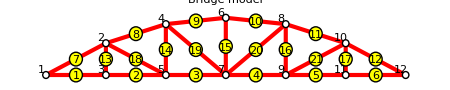

Bridge DOF Activity:

node | x-tag | y-tag | z-tag | x-value | y-value | z-value
1 |  1 |  1 |  1 |  0 |  0 |  0
2 |  0 |  0 |  1 |  0 |  0 |  0
3 |  0 |  0 |  1 |  0 | -10 |  0
4 |  0 |  0 |  1 |  0 |  0 |  0
5 |  0 |  0 |  1 |  0 | -10 |  0
6 |  0 |  0 |  1 |  0 |  0 |  0
7 |  0 |  0 |  1 |  0 | -16 |  0
8 |  0 |  0 |  1 |  0 |  0 |  0
9 |  0 |  0 |  1 |  0 | -10 |  0
10 |  0 |  0 |  1 |  0 |  0 |  0
11 |  0 |  0 |  1 |  0 | -10 |  0
12 |  0 |  1 |  1 |  0 |  0 |  0

Bridge computed node displacements:

node | x-displ | y-displ | z-displ
1 |       0 |       0 |       0
2 |  0.809536 | -1.775600 |       0
3 |  0.280000 | -1.792260 |       0
4 |  0.899001 | -2.291930 |       0
5 |  0.560000 | -2.316600 |       0
6 |  0.847500 | -2.385940 |       0
7 |  0.847500 | -2.421940 |       0
8 |  0.795999 | -2.291930 |       0
9 |  1.135000 | -2.316600 |       0
10 |  0.885464 | -1.775600 |       0
11 |  1.415000 | -1.792260 |       0
12 |  1.695000 |       0 |       0

Bridge node forces including reactions:

node | x-force | y-force | z-force
1 |     0 |  28.0000 |     0
2 |     0 |     0 |     0
3 |     0 | -10.0000 |     0
4 |     0 |     0 |     0
5 |     0 | -10.0000 |     0
6 |     0 |     0 |     0
7 |     0 | -16.0000 |     0
8 |     0 |     0 |     0
9 |     0 | -10.0000 |     0
10 |     0 |     0 |     0
11 |     0 | -10.0000 |     0
12 |     0 |  28.0000 |     0

Bridge int forces and stresses:

elem | axial force | axial stress
1 |  56.0000 |  28.0000
2 |  56.0000 |  28.0000
3 |  57.5000 |  28.7500
4 |  57.5000 |  28.7500
5 |  56.0000 |  28.0000
6 |  56.0000 |  28.0000
7 | -62.6100 | -6.2610
8 | -60.0300 | -6.0030
9 | -60.3000 | -6.0300
10 | -60.3000 | -6.0300
11 | -60.0300 | -6.0030
12 | -62.6100 | -6.2610
13 |  10.0000 |  3.3330
14 |  9.2500 |  3.0830
15 |  12.0000 |  4.0000
16 |  9.2500 |  3.0830
17 |  10.0000 |  3.3330
18 |  1.6770 |  1.6770
19 |  3.2020 |  3.2020
20 |  3.2020 |  3.2020
21 |  1.6770 |  1.6770

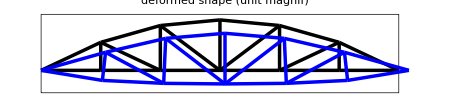

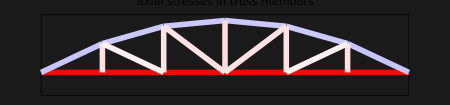

```mathematica
NodeCoordinates={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
            {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
ElemNodes={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
           {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
           {2,3},{4,5},{6,7},{8,9},{10,11},
           {2,5},{4,7},{7,8},{9,10}};
PrintSpaceTrussNodeCoordinates[NodeCoordinates,"Node coordinates:",{}];            
numnod=Length[NodeCoordinates];  numele=Length[ElemNodes];
Em=1000; Abot=2; Atop=10; Abat=3; Adia=1; 
ElemMaterials= Table[Em,{numele}]; 
ElemFabrications={Abot,Abot,Abot,Abot,Abot,Abot,Atop,Atop,Atop,Atop,
                  Atop,Atop,Abat,Abat,Abat,Abat,Abat,Adia,Adia,Adia,Adia}; 
PrintSpaceTrussElementData[ElemNodes,ElemMaterials,ElemFabrications,
           "Element data:",{}]; 
ProcessOptions= {True};

view={{0,1,0},{0,0,1}}; imgsiz=450;
labels={{True,0.06,-1.5,1.5},{True,0.12},{"Times",11,"Roman"}};
PlotSpaceTrussElementsAndNodes[NodeCoordinates,ElemNodes,
    "Bridge model",{view,-1,imgsiz,labels}];
  
NodeDOFTags=  Table[{0,0,1},{numnod}];
NodeDOFValues=Table[{0,0,0},{numnod}]; 
NodeDOFValues[[3]]={0,-10,0}; NodeDOFValues[[5]]= {0,-10,0}; 
NodeDOFValues[[7]]={0,-16,0};  
NodeDOFValues[[9]]={0,-10,0}; NodeDOFValues[[11]]={0,-10,0}; 
NodeDOFTags[[1]]= {1,1,1};     (* fixed node 1 *)
NodeDOFTags[[numnod]]={0,1,1}; (* hroller @ node 12 *)
PrintSpaceTrussFreedomActivity[NodeDOFTags,NodeDOFValues,
       "Bridge DOF Activity:",{}];

{NodeDisplacements,NodeForces,ElemForces,ElemStresses}=
   SpaceTrussSolution[ NodeCoordinates,ElemNodes,ElemMaterials,
   ElemFabrications,NodeDOFTags,NodeDOFValues,ProcessOptions ];
   
PrintSpaceTrussNodeDisplacements[NodeDisplacements,
      "Bridge computed node displacements:",{}];
PrintSpaceTrussNodeForces[NodeForces,
      "Bridge node forces including reactions:",{}];
PrintSpaceTrussElemForcesAndStresses[ElemForces,ElemStresses,
      "Bridge int forces and stresses:",{}];
      
view={{0,1,0},{0,0,1}}; box={{0,-4,0},{60,-4,0},{60,10,0},{0,10,0}};
PlotSpaceTrussDeformedShape[NodeCoordinates,ElemNodes,NodeDisplacements,
  {0,1},box,"deformed shape (unit magnif)",{view,-1,imgsiz,{"black","blue"}}];      
PlotSpaceTrussStresses[NodeCoordinates,ElemNodes,ElemStresses,1,box,
  "axial stresses in truss members",{view,0,imgsiz,labels}];
```

Cell 8B.  Animation of deflections  -- for versions >=9 -- still does not work

```mathematica
view={{0,1,0},{0,0,1}}; box={{0,-4,0},{65,-4,0},{65,10,0},{0,10,0}};
Manipulate[
    PlotSpaceTrussDeformedShape[NodeCoordinates,ElemNodes,
    NodeDisplacements,amp,box,"deformed bridge animation",
    {view,-1,"red"}],{amp,0,1}];
```

Cell 9.     25-member transmission tower driver script for HW Exercise 21.5  
Recommended setting for preprocessor plot data:
  imgsiz=360; view={{0,0,1},{1,-3,1}};
  labels={{True,0.014,-1.5,1.5},{True,0.020},{"Times",12,"Roman"}};
  Recommended setting for postprocessor plot data:
  view={{0,0,1},{2,-3,1}};
  box={{-100,100,0},{100,100,0},{100,-100,0},{-100,-100,0},
           {-100,100,200},{100,100,200},{100,-100,200},{-100,-100,200}};
  No change for imgsiz and labels

Node coordinates:

node | x-coor | y-coor | z-coor
1 | -37.500000 |       0 |     200
2 |  37.500000 |       0 |     200
3 | -37.500000 |  37.500000 |     100
4 |  37.500000 |  37.500000 |     100
5 |  37.500000 | -37.500000 |     100
6 | -37.500000 | -37.500000 |     100
7 |    -100 |     100 |       0
8 |     100 |     100 |       0
9 |     100 |    -100 |       0
10 |    -100 |    -100 |       0

Element data:

elem | nodes | modulus | area
1 | {1, 2} |  10000000 |    0.033
2 | {1, 4} |  10000000 |    2.015
3 | {2, 3} |  10000000 |    2.015
4 | {1, 5} |  10000000 |    2.015
5 | {2, 6} |  10000000 |    2.015
6 | {2, 4} |  10000000 |    2.823
7 | {2, 5} |  10000000 |    2.823
8 | {1, 3} |  10000000 |    2.823
9 | {1, 6} |  10000000 |    2.823
10 | {3, 6} |  10000000 |    0.010
11 | {4, 5} |  10000000 |    0.010
12 | {3, 4} |  10000000 |    0.014
13 | {5, 6} |  10000000 |    0.014
14 | {3, 10} |  10000000 |    0.980
15 | {6, 7} |  10000000 |    0.980
16 | {4, 9} |  10000000 |    0.980
17 | {5, 8} |  10000000 |    0.980
18 | {4, 7} |  10000000 |    1.760
19 | {3, 8} |  10000000 |    1.760
20 | {5, 10} |  10000000 |    1.760
21 | {6, 9} |  10000000 |    1.760
22 | {6, 10} |  10000000 |    2.440
23 | {3, 7} |  10000000 |    2.440
24 | {5, 9} |  10000000 |    2.440
25 | {4, 8} |  10000000 |    2.440

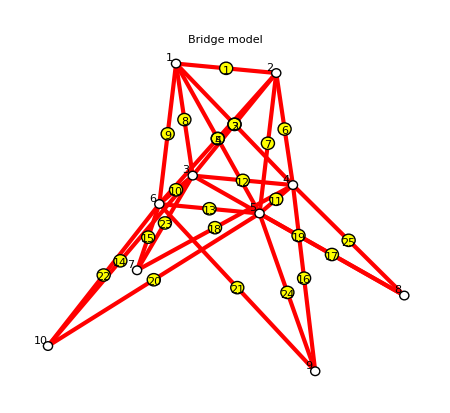

Bridge DOF Activity:

node | x-tag | y-tag | z-tag | x-value | y-value | z-value
1 |  0 |  0 |  0 |  1000 |  10000 | -5000
2 |  0 |  0 |  0 |  0 |  10000 | -5000
3 |  0 |  0 |  0 |  500 |  0 |  0
4 |  0 |  0 |  0 |  0 |  0 |  0
5 |  0 |  0 |  0 |  0 |  0 |  0
6 |  0 |  0 |  0 |  500 |  0 |  0
7 |  1 |  1 |  1 |  0 |  0 |  0
8 |  1 |  1 |  1 |  0 |  0 |  0
9 |  1 |  1 |  1 |  0 |  0 |  0
10 |  1 |  1 |  1 |  0 |  0 |  0

Bridge computed node displacements:

node | x-displ | y-displ | z-displ
1 |  0.008515 |  0.349956 | -0.022128
2 |  0.031916 |  0.349956 | -0.032242
3 |  0.011530 | -0.009770 | -0.108526
4 | -0.004039 | -0.008781 | -0.115393
5 |  0.000448 | -0.005089 |  0.070508
6 |  0.007042 | -0.004100 |  0.077375
7 |       0 |       0 |       0
8 |       0 |       0 |       0
9 |       0 |       0 |       0
10 |       0 |       0 |       0

Bridge node forces including reactions:

node | x-force | y-force | z-force
1 |  1000.00 |  10000.00 | -5000.00
2 |       0 |  10000.00 | -5000.00
3 |   500.00 |       0 |       0
4 |       0 |       0 |       0
5 |       0 |       0 |       0
6 |   500.00 |       0 |       0
7 |  9907.89 | -6262.79 |  11750.00
8 | -10907.90 | -7326.28 |  13250.00
9 |  5665.14 | -2673.72 | -6750.00
10 | -6665.14 | -3737.21 | -8250.00

Bridge int forces and stresses:

elem | axial force | axial stress
1 |   102.96 |  3120.07
2 | -5995.74 | -2975.55
3 | -5125.72 | -2543.78
4 |  4076.53 |  2023.09
5 |  4946.56 |  2454.87
6 | -12715.30 | -4504.18
7 |  7521.91 |  2664.51
8 | -12003.30 | -4251.96
9 |  8233.91 |  2916.72
10 |    -7.56 |  -755.95
11 |    -4.92 |  -492.25
12 |   -29.06 | -2075.88
13 |   -12.31 |  -879.30
14 | -3427.31 | -3497.25
15 |  2610.77 |  2664.05
16 | -3731.60 | -3807.75
17 |  2306.47 |  2353.54
18 | -6192.99 | -3518.74
19 | -6343.94 | -3604.51
20 |  3644.32 |  2070.64
21 |  3493.37 |  1984.87
22 |  10850.80 |  4447.07
23 | -13042.60 | -5345.34
24 |  9184.31 |  3764.06
25 | -14709.20 | -6028.34

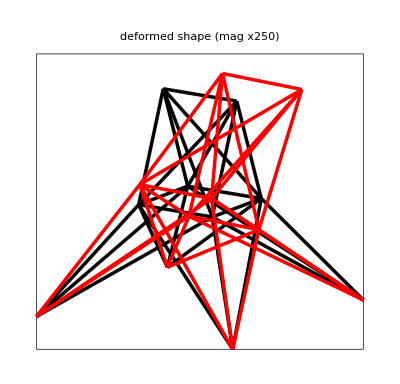

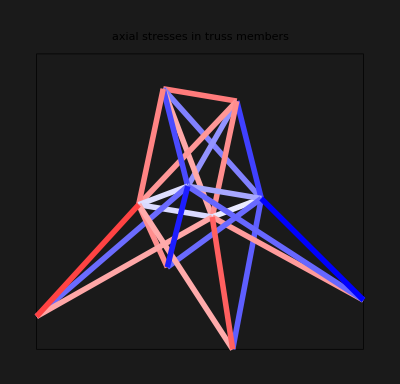

```mathematica
NodeCoordinates={{-37.5,0,200},{37.5,0,200},{-37.5,37.5,100},{37.5,37.5,100},{37.5,-37.5,100},{-37.5,-37.5,100},
            {-100,100,0},{100,100,0},{100,-100,0},{-100,-100,0}};
ElemNodes={{1,2},{1,4},{2,3},{1,5},{2,6},{2,4},{2,5},{1,3},{1,6},
{3,6},{4,5},{3,4},{5,6},{3,10},{6,7},{4,9},{5,8},{4,7},{3,8},{5,10},{6,9},{6,10},{3,7},{5,9},{4,8}};
PrintSpaceTrussNodeCoordinates[NodeCoordinates,"Node coordinates:",{}];            
numnod=Length[NodeCoordinates];  numele=Length[ElemNodes];
Em=10000000; A1=0.033; A2=2.015; A3=2.823; A4=0.01; A5=0.014; A6=0.98; A7=1.760; A8=2.44; 
ElemMaterials= Table[Em,{numele}]; 
ElemFabrications={A1,A2,A2,A2,A2,A3,A3,A3,A3,A4,A4,A5,A5,A6,A6,A6,A6,A7,A7,A7,A7,A8,A8,A8,A8}; 
PrintSpaceTrussElementData[ElemNodes,ElemMaterials,ElemFabrications,
           "Element data:",{}]; 
ProcessOptions= {True};

view={{0,0,1},{1,-3,1}}; imgsiz=450;
labels={{True,0.014,-1.5,1.5},{True,0.02},{"Times",12,"Roman"}};
PlotSpaceTrussElementsAndNodes[NodeCoordinates,ElemNodes,
    "Bridge model",{view,-1,imgsiz,labels}];
  
NodeDOFTags=  Table[{0,0,0},{numnod}];
NodeDOFValues=Table[{0,0,0},{numnod}]; 
NodeDOFValues[[1]]={1000,10000,-5000}; NodeDOFValues[[2]]={0,10000,-5000};
NodeDOFValues[[3]]={500,0,0}; NodeDOFValues[[6]]={500,0,0};
NodeDOFTags[[7]]= {1,1,1}; NodeDOFTags[[8]]= {1,1,1};
NodeDOFTags[[9]]= {1,1,1}; NodeDOFTags[[10]]= {1,1,1};
PrintSpaceTrussFreedomActivity[NodeDOFTags,NodeDOFValues,
       "Bridge DOF Activity:",{}];

{NodeDisplacements,NodeForces,ElemForces,ElemStresses}=
   SpaceTrussSolution[ NodeCoordinates,ElemNodes,ElemMaterials,
   ElemFabrications,NodeDOFTags,NodeDOFValues,ProcessOptions ];
   
PrintSpaceTrussNodeDisplacements[NodeDisplacements,
      "Bridge computed node displacements:",{}];
PrintSpaceTrussNodeForces[NodeForces,
      "Bridge node forces including reactions:",{6,2}];
PrintSpaceTrussElemForcesAndStresses[ElemForces,ElemStresses,
      "Bridge int forces and stresses:",{6,2}];
      
view={{0,0,1},{2,-3,1}}; imgsiz=400;
box={{-100,100,0},{100,100,0},{100,-100,0},{-100,-100,0},
           {-100,100,200},{100,100,200},{100,-100,200},{-100,-100,200}};
PlotSpaceTrussDeformedShape[NodeCoordinates,ElemNodes,NodeDisplacements,
  {0,250},box,"deformed shape (mag x250)",{view,-1,imgsiz,{"black","red"}}];      
PlotSpaceTrussStresses[NodeCoordinates,ElemNodes,ElemStresses,1,box,
  "axial stresses in truss members",{view,0,imgsiz,labels}];
```

Cell 10. Module to compute space truss weight as model check. Run only after model is defined in previous cell

```mathematica
SpaceTrussWeight[nodxyz_,elenod_,elefab_,specw_]:=Module[
{e,ni,nj,w=0,x1,x2,y1,y2,z1,z2,x21,y21,z21,
  numele=Length[elenod],LL},
  For [e=1,e<=numele,e++,  {ni,nj}=elenod[[e]]; 
       ncoor={nodxyz[[ni]],nodxyz[[nj]]};  
       {{x1,y1,z1},{x2,y2,z2}}=ncoor; 
       {x21,y21,z21}={x2-x1,y2-y1,z2-z1};LL=x21^2+y21^2+z21^2;
       w+=Sqrt[LL]*elefab[[e]]*specw];
  Return[w]];    
    
w=SpaceTrussWeight[NodeCoordinates,ElemNodes,ElemFabrications,0.1]; 
Print["truss weight=",w];
```

truss weight=555.184